## Figure 5A, 5B

Evaluate notebook to generate plots for Fig. 5A and 5B, showing multistability in a two-species competition. 5A uses α_11=0.29, whereas 5B uses α_11=0.31. They also have different relevant ranges of α_21. This code is sufficient to generate all the fixed points itself, but it’s faster to do this once and import the data later.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### functions

```mathematica
getConcentration[n_,nutrient_,α_]:=
Block[{i,m0,c,dc,m,cSystem,dcSys,dcSysWrap1,dcSysWrap2,dcSystem,totalcSys,vars,aVars,bVars,z},
m0=Length[n];
aVars=ToExpression[Table["a"<>IntegerString[k],{k,m0}]];
bVars=ToExpression[Table["b"<>IntegerString[k],{k,m0}]];
c[a_,b_,alpha_,θ_]:=a*E^(Sqrt[alpha/d]*θ)+b*E^(-Sqrt[alpha/d]*θ)+s[[nutrient]]/alpha;
dc[a_,b_,alpha_,θ_]:=Sqrt[alpha/d]*(a*E^(Sqrt[alpha/d]*θ)-b*E^(-Sqrt[alpha/d]*θ));

(*  Create a system of eqs for c(θ) in each region *)
cSys=Table[c[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==c[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
cSysWrap=c[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==c[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
cSystem=Join[cSys,{cSysWrap}];

(*do the same thing for the derivatives of c(θ)*)
dcSys=Table[dc[aVars[[i]],bVars[[i]],α[[i,nutrient]],n[[i]]]==dc[aVars[[i+1]],bVars[[i+1]],α[[i+1,nutrient]],0],{i,m0-1}];
dcSysWrap=dc[aVars[[m0]],bVars[[m0]],α[[m0,nutrient]],n[[m0]]]==dc[aVars[[1]],bVars[[1]],α[[1,nutrient]],0];
dcSystem=Join[dcSys,{dcSysWrap}];


totalcSys=Join[cSystem,dcSystem];
vars=Table[{aVars[[i]],bVars[[i]]},{i,m0}]//Flatten;
{z,m}=CoefficientArrays[totalcSys,vars];
LinearSolve[m,-z]  
];
(*returns {a1,b1,a2,b2...}: in a region σ c_i=a*E^(a*θ/d)+b*E^(-a*θ/d)+si/αi. *)
```

```mathematica
getGrowth[pop_,species_,c_,α_]:=
Block[{growth,myN,myA,myB},
myN=pop[[species]];
myA=c[[species*2-1]];
myB=c[[species*2]];

growth=Table[α[[species,i]]*((s[[i]]*myN/α[[species,i]])+Sqrt[d/α[[species,i]]]*(myA[[i]]*(E^(myN*Sqrt[α[[species,i]]/d])-1)-myB[[i]]*(E^(-myN*Sqrt[α[[species,i]]/d])-1))),{i,2}]//Total
];
```

```mathematica
ndot[n1_,α_]:=
Block[{dn,growthTable,n0,nNew,cCoeff},
n0={n1,L-n1};
cCoeff=Transpose[{getConcentration[n0,1,α],getConcentration[n0,2,α]}];
growthTable=Table[getGrowth[n0,i,cCoeff,α],{i,Length[n0]}];
(*δ=Total[growthTable];*)
dn=growthTable-δ*n0//First
];
```

### parameters

```mathematica
s1=0.3;
s2=1-s1;
s={s1,s2};
d=1;
L=20;
e=1;
δ=1;
```

### root function: given two strategies, what are non-trivial roots?

```mathematica
roots[strat1_,strat2_]:=
Block[{α,rootList,uniqueList,count},
α={{strat1,e-strat1},{strat2,e-strat2}};
rootList=Table[x/.Quiet[Check[FindRoot[ndot[x,α],{x,i,0,L}],x->-1]],{i,0,L,.5}];
uniqueList=Union[rootList,SameTest->(Abs[#1-#2]≤10^-3&)];
DeleteCases[uniqueList,-1]
];
```

### 5A: bistable coexistence

```mathematica
strat2Range={.43,.445};
```

```mathematica
(*can either calculate roots using this line, which takes a few minutes, or import the data in the line below.*)
(*rootList=Table[roots[.29,i],{i,strat2Range[[1]],strat2Range[[2]],.0001}]*)
```

```mathematica
rootList=Import["data//rootList_5A_s1=0.3_alpha1=0.29_d1_l20_pbc.mx"];
```

remove trivial roots 0, L

```mathematica
removeZero=Table[DeleteCases[rootList[[i]],x_/;x<=0.],{i,Length[rootList]}];
removeL=Table[DeleteCases[removeZero[[i]],x_/;x≥L],{i,Length[rootList]}];
trivialRemoved=DeleteCases[removeL,{}];
```

#### prepare cases with multistability

```mathematica
split=Cases[trivialRemoved,x_List/;Length[x]==3];       (*all multistable points*)
splitPositions=Position[trivialRemoved,x_List/;Length[x]==3]//Flatten;
```

```mathematica
xAxis=Range[strat2Range[[1]],strat2Range[[2]],.0001];
splitAxis=Table[xAxis[[splitPositions[[i]]]],{i,Length[splitPositions]}];
```

```mathematica
lowerBranch=First/@split;
upperBranch=Last/@split;
middleBranch=split[[;;,2]];
```

```mathematica
upperPairs=Transpose[{splitAxis,upperBranch}];
lowerPairs=Transpose[{splitAxis,lowerBranch}];
middlePairs=Transpose[{splitAxis,middleBranch}];
```

```mathematica
unique=Cases[trivialRemoved,x_List/;Length[x]==1]//Flatten;
uniquePositions=Position[trivialRemoved,x_List/;Length[x]==1]//Flatten;
```

```mathematica
uniqueAxis=Table[xAxis[[uniquePositions[[i]]]],{i,Length[uniquePositions]}];
uniquePairs=Transpose[{uniqueAxis,unique}];
```

```mathematica
leftBoundary=splitAxis//First;
rightBoundary=splitAxis//Last;
```

```mathematica
labels={Graphics[Text[ToString[leftBoundary],{leftBoundary-.0003,2.8}]],Graphics[Text[ToString[rightBoundary],{rightBoundary-.0003,2.8}]]};
```

now rescale fixed points to be in units of L

```mathematica
scaledLowerPairs=Table[{lowerPairs[[i,1]],lowerPairs[[i,2]]/L},{i,Length[lowerPairs]}];
scaledUpperPairs=Table[{upperPairs[[i,1]],upperPairs[[i,2]]/L},{i,Length[upperPairs]}];
scaledMiddlePairs=Table[{middlePairs[[i,1]],middlePairs[[i,2]]/L},{i,Length[middlePairs]}];
scaledUniquePairs=Table[{uniquePairs[[i,1]],uniquePairs[[i,2]]/L},{i,Length[uniquePairs]}];
```

```mathematica
cutoff=Position[Table[scaledUniquePairs[[i+1,1]]-scaledUniquePairs[[i,1]],{i,Length[scaledUniquePairs]-1}],Max[Table[scaledUniquePairs[[i+1,1]]-scaledUniquePairs[[i,1]],{i,Length[scaledUniquePairs]-1}]]]//Flatten;
```

```mathematica
scaledStableLower=SortBy[Join[scaledLowerPairs,scaledUniquePairs[[1;;cutoff[[1]]]]],First];
scaledStableUpper=SortBy[Join[scaledUpperPairs,scaledUniquePairs[[cutoff[[1]]+1;;-1]]],First];
```

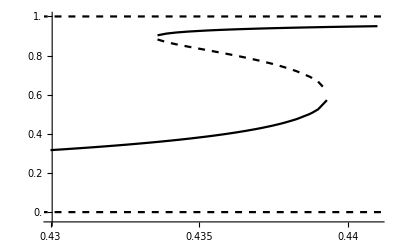

```mathematica
Show[ListPlot[{scaledStableLower,scaledStableUpper,scaledMiddlePairs},PlotRange->{{.43,.441},{-.05,1}},TicksStyle->Black,Ticks->{{.43,.435,.44},Range[0,1,.2]},Joined->True,PlotStyle->{Black,Directive[Black],Directive[Black,Dashed]},AxesOrigin->{Automatic,-.05}],Plot[{1,0},{x,.3,.5},PlotStyle->{Directive[Black,Dashed],Directive[Black,Dashed]},AxesOrigin->{Automatic,-.05}],LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig5A_bistability.svg",%];
```

### 5B: bistable exclusion and the Allee effect

```mathematica
strat2Range={.36,.44};
```

```mathematica
(*can either calculate roots using this line, which takes a few minutes, or import the data in the line below.*)
(*rootList=Table[roots[.31,i],{i,strat2Range[[1]],strat2Range[[2]],.0001}]*)
```

```mathematica
rootList=Import["data//rootList_5B_s1=0.3_alpha1=0.31_d1_l20_pbc.mx"];
```

```mathematica
a2Range=Range[strat2Range[[1]],strat2Range[[2]],.0001];
```

```mathematica
removeMisses=rootList;
newRange=a2Range;
```

```mathematica
(*when there are 4, remove 0 and L
when there are 1 or 2, just make it L*)
```

```mathematica
For[i=1,i≤Length[removeMisses],i++,
If[Length[removeMisses[[i]]]>2,removeMisses[[i]]=DeleteCases[removeMisses[[i]],x_/;x<=0.||x≥(L-.0001)],removeMisses[[i]]={L}]
]
```

```mathematica
annihilationPos=FirstPosition[removeMisses,x_?VectorQ/;Length[x]==1]//First;
```

```mathematica
lowerBranch=First/@removeMisses[[1;;annihilationPos-1]];
upperBranch=Last/@removeMisses[[1;;annihilationPos-1]];
```

```mathematica
upperPairs=Transpose[{newRange[[1;;annihilationPos-1]],upperBranch}];
lowerPairs=Transpose[{newRange[[1;;annihilationPos-1]],lowerBranch}];
```

```mathematica
scaledUpperPairs=Table[{upperPairs[[i,1]],upperPairs[[i,2]]/L},{i,Length[upperPairs]}];
scaledLowerPairs=Table[{lowerPairs[[i,1]],lowerPairs[[i,2]]/L},{i,Length[lowerPairs]}];
```

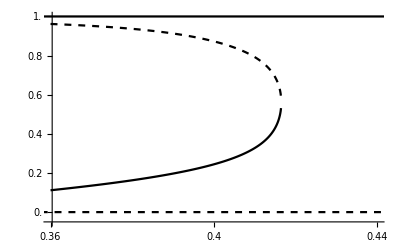

```mathematica
Show[ListPlot[{scaledLowerPairs,scaledUpperPairs},PlotRange->{{.36,.44},{-.05,1}},TicksStyle->Black,Ticks->{Range[.36,.46,.02],Range[0,1,.2]},AxesOrigin->{Automatic,-.05},Joined->True,PlotStyle->{Black,Directive[Dashed,Black]}],Plot[{1,0},{x,.3,.5},PlotStyle->{Black,Directive[Black,Dashed]},AxesOrigin->{Automatic,-.05}],LabelStyle->{FontSize->12}]
```

```mathematica
Export["fig5B_alleeEffect.svg",%];
```